1.1. Пробел выполняет роль знака умножения.

```mathematica
3 6
```

18

1.2. Введение дополнительных пробелов не изменяет результат вычислений.

```mathematica
3      6
```

18

1.3. Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.

```mathematica
12^(1/(1+1))
```

2 √3

```mathematica
N[12^(1/(1+1))]
```

3.4641

```mathematica
3/7
```

3/7

```mathematica
N[3/7]
```

0.428571

1.4. Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.

```mathematica
12.^(1/(1+1))
```

3.4641

```mathematica
3./7
```

0.428571

1.5. Для изменения стандартного порядка выполнения операций используются скобки.

```mathematica
2*2+2
```

6

```mathematica
2*(2+2)
```

8

2.1. С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Проверить точность с помощью Precision.

```mathematica
N[17^(1/2),200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

2.2. Найти приближенное значение числа с точностью до 40 значащих цифр.

```mathematica
N[e^(x *Sqrt[163]), 40]
```

e^(12.76714533480370466171095200978089234738 x)

2.3. Вычислить.

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

2.4. Введите выражения.

```mathematica
5>3
```

True

```mathematica
5<2
```

False

2.5. Определите, справедливо или нет неравенство.

```mathematica
π^ⅇ>ⅇ^π
```

False

```mathematica
N[π^ⅇ]
```

22.4592

```mathematica
N[ⅇ^π]
```

23.1407

3.1. Решить уравнения.

```mathematica
NSolve[√(x+2)+4  x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

3.2. Решить системы уравнений.

```mathematica
NSolve[{x^2+x y+y^2==1, x^3+x^2 y+x y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3z == 34, x+y-z==-1, -x+2y+3z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

3.3. Придумать свою систему уравнений.

```mathematica
NSolve[{(4 x^2+y^2+4 y)/(y^2-4y)==4, x^3 y+y^4+x^4== 48}, {x,y}]
```

{{x→-0.0469283-3.60646 ⅈ,y→3.24297-2.49724 ⅈ},{x→-0.0469283+3.60646 ⅈ,y→3.24297+2.49724 ⅈ},{x→-2.39966,y→-1.00129},{x→2.23419-4.52611 ⅈ,y→0.246379+4.36771 ⅈ},{x→2.23419+4.52611 ⅈ,y→0.246379-4.36771 ⅈ},{x→-0.242495-2.43791 ⅈ,y→1.47718-0.424665 ⅈ},{x→-0.242495+2.43791 ⅈ,y→1.47718+0.424665 ⅈ},{x→3.03624,y→-1.50431}}

4. Найти решение уравнения, используя функцию FindRoot .

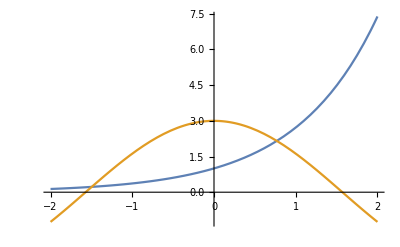

```mathematica
Plot[{ⅇ^x, 3Cos[x]}, {x, -2,2}]
```

```mathematica
FindRoot[ⅇ^x==3Cos[x],{x,-1.5}]
```

{x→-1.49606}

```mathematica
FindRoot[ⅇ^x==3Cos[x],{x,0.7}]
```

{x→0.768579}

5. Найти решение дифференциального уравнения.

```mathematica
sol=NDSolve[{y''[x]+y[x]x-Cos[2x]==0, y[0]==0, y'[0]==2},y, {x,0,5}]
```

{{y→InterpolatingFunction[…]}}

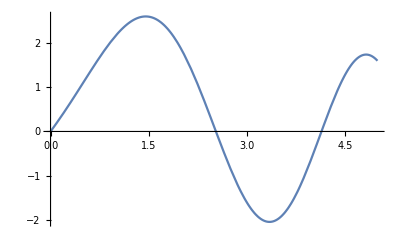

```mathematica
Plot[y[x]/.sol,{x,0,5}]
```

```mathematica
sol1=FindRoot[(y[x]/.sol)==0,{x,0}]
```

{x→0.}

```mathematica
sol2=FindRoot[(y[x]/.sol)==0,{x,2.5}]
```

{x→2.52928}

```mathematica
sol3=FindRoot[(y[x]/.sol)==0,{x,4.2}]
```

{x→4.14386}

```mathematica
D[y[x]/.sol,x]/.sol1
```

{2.}

```mathematica
D[y[x]/.sol,x]/.sol2
```

{-3.91734}

```mathematica
D[y[x]/.sol,x]/.sol3
```

{4.02341}

```mathematica
sol4=FindRoot[D[y[x]/.sol,x]==0, {x,3.3}]
```

{x→3.3488}

```mathematica
y[x]/.sol/.sol4
```

{-2.04443}

```mathematica
FindMinimum[y[x]/.sol, {x,3.3}]
```

{-2.04443,{x→3.3488}}

6. Обработка численных данных.

```mathematica
task1 = Table[{x,(21+52x+73 x^2+17 x^3+33 x^4)(1+Random[Real, {-0.2,0.2}])}, {x,0,5,0.25}]
```

{{0.,23.673},{0.25,35.9691},{0.5,68.5616},{0.75,110.396},{1.,230.357},{1.25,313.66},{1.5,436.966},{1.75,601.918},{2.,1234.9},{2.25,1316.11},{2.5,2186.13},{2.75,3170.77},{3.,3414.65},{3.25,5578.43},{3.5,6010.38},{3.75,8136.84},{4.,10223.5},{4.25,12807.2},{4.5,19178.4},{4.75,22460.9},{5.,22594.9}}

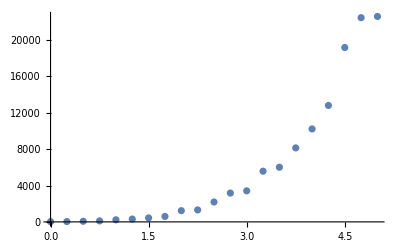

```mathematica
task1Plot=ListPlot[task1]
```

```mathematica
task1Fit=Fit[task1, {1,x,x^2, x^3, x^4},x]
```

-255.607+1729.63 x-1661.96 x^2+583.747 x^3-24.5944 x^4

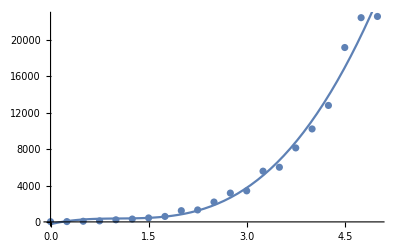

```mathematica
Show[task1Plot, Plot[task1Fit, {x,0,5}]]
```

```mathematica
task2 = Table[{x,(21+42x+84Sin[x]+35Cos[x])(1+Random[Real, {-0.1, 0.1}])}, {x,0,5,0.25}]
```

{{0.,58.2093},{0.25,83.704},{0.5,113.375},{0.75,134.131},{1.,149.207},{1.25,176.967},{1.5,159.762},{1.75,171.468},{2.,179.84},{2.25,163.546},{2.5,137.781},{2.75,140.574},{3.,130.748},{3.25,104.962},{3.5,105.054},{3.75,101.928},{4.,94.2447},{4.25,117.455},{4.5,111.328},{4.75,128.776},{5.,168.278}}

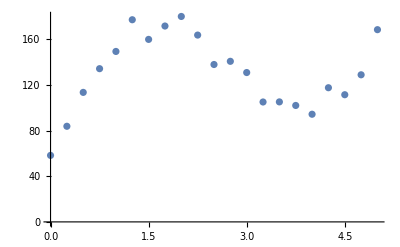

```mathematica
task2Plot=ListPlot[task2]
```

```mathematica
task2Fit=Fit[task2, {1,x,Cos[x], Sin[x]},x]
```

18.0235+43.0562 x+36.1875 Cos[x]+87.4128 Sin[x]

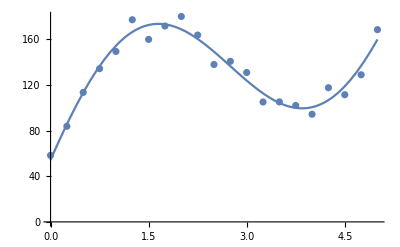

```mathematica
Show[task2Plot, Plot[task2Fit, {x,0,5}]]
```